# Q4

Set::write: Tag Graphics in ()[x_] is Protected.

π/4+(x-1)/2+O[x-1]^2

π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3+O[x-1]^4

π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3-1/40 (x-1)^5+O[x-1]^6

π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3-1/40 (x-1)^5+1/48 (x-1)^6-1/112 (x-1)^7+O[x-1]^8

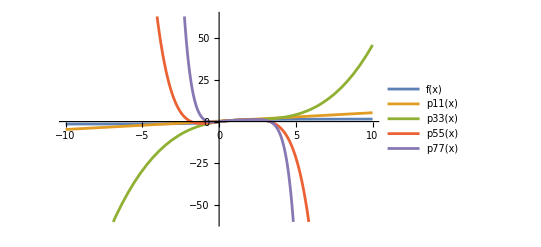

```mathematica
f[x_]:=ArcTan[x];
p1[x_]=Series[ArcTan[x],{x,1,1}]
p3[x_]=Series[ArcTan[x],{x,1,3}]
p5[x_]=Series[ArcTan[x],{x,1,5}]
p7[x_]=Series[ArcTan[x],{x,1,7}]
p11[x_]:=π/4+(x-1)/2
p33[x_]:=π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3
p55[x_]:=π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3-1/40 (x-1)^5
p77[x_]:=π/4+(x-1)/2-1/4 (x-1)^2+1/12 (x-1)^3-1/40 (x-1)^5+1/48 (x-1)^6-1/112 (x-1)^7
Plot[
{f[x],p11[x],p33[x],p55[x],p77[x]},
{x,-10,10},
PlotLegends->"Expressions"
]
```